```mathematica
s1[n_,s_]:=Sum[j^s,{j,1,n}]-Integrate[j^s,{j,0,n}]-n^s/2
s2[n_,s_]:=Sum[j^(s I)/j^(1/2),{j,1,n}]-Integrate[j^(s I)/j^(1/2),{j,0,n}]-n^(s I)/n^(1/2)/2
s3[n_,s_]:=Sum[E^(s Log[j] I)/j^(1/2),{j,1,n}]-Integrate[E^(s Log[j] I)/j^(1/2),{j,0,n}]-E^((s I-1/2)Log[n])/2
s4[n_,s_]:=1+Sum[Sum[(s Log[j] I)^k/k!,{k,0,Infinity}]/j^(1/2),{j,2,n}]-Integrate[E^(s Log[j] I)/j^(1/2),{j,0,n}]-E^((s I)Log[n])/n^(1/2)/2
s4a[n_,s_]:=(1/2-ⅈ s)(1-((2 ⅈ)/(ⅈ-2 s))+Sum[Sum[(s Log[j] I)^k/k!,{k,0,Infinity}]/j^(1/2),{j,2,n}]-Integrate[E^(s Log[j] I)/j^(1/2),{j,1,n}]-E^((s I)Log[n])/n^(1/2)/2)
s5[n_,s_]:=1+Sum[Sum[(s Log[j] I)^k/k!,{k,0,Infinity}]/j^(1/2),{j,2,n}]-Integrate[Sum[(s Log[j] I)^k/k!,{k,0,Infinity}]/j^(1/2),{j,0,n}]-Sum[((s I)Log[n])^k/k!,{k,0,Infinity}]/n^(1/2)/2
s6[n_,s_]:=1+ Sum[ Sum[(I s)^k(Log[j])^k/k!,{k,0,Infinity}]/j^(1/2),{j,2,n}]-Integrate[Sum[(I s)^k( Log[j] )^k/k!,{k,0,Infinity}]/j^(1/2),{j,0,n}]-Sum[(s I)^k(Log[n])^k/k!,{k,0,Infinity}]/n^(1/2)/2
s7[n_,s_, l_]:=1+ Sum[ Sum[(I s)^k(Log[j])^k/k!,{k,0,l}]/j^(1/2),{j,2,n}]-Integrate[Sum[(I s)^k( Log[j] )^k/k!,{k,0,l}]/j^(1/2),{j,0,n}]-Sum[(s I)^k(Log[n])^k/k!,{k,0,l}]/n^(1/2)/2
s8[n_,s_, l_]:=(1/2-ⅈ s)(1+ Sum[Sum[(I s)^k(Log[j])^k/k!/j^(1/2),{j,2,n}]-Integrate[(I s)^k( Log[j] )^k/k!/j^(1/2),{j,0,n}]-(s I)^k(Log[n])^k/k!/n^(1/2)/2,{k,0,l}])
s9[n_,s_, l_]:=(1/2-ⅈ s)(1+ Sum[(I s)^k/k!Sum[(Log[j])^k/j^(1/2),{j,2,n}]-(I s)^k/k!Integrate[( Log[j] )^k/j^(1/2),{j,0,n}]-(s I)^k/k!(Log[n])^k/n^(1/2)/2,{k,0,l}])
s10[n_,s_, l_]:=(1/2-ⅈ s)(1-((2 ⅈ)/(ⅈ-2 s))+ Sum[(I s)^k/k!(Sum[Log[j]^k/j^(1/2),{j,2,n}]-Integrate[ Log[j]^k/j^(1/2),{j,1,n}]-Log[n]^k/n^(1/2)/2),{k,0,l}])
s11[n_,s_, l_]:=(1/2-ⅈ s)(1-((2 ⅈ)/(ⅈ-2 s))+ Sum[(I s)^k/k!(Sum[Log[j]^k/j^(1/2),{j,2,n}]-((-2)^(1+k) (Gamma[1+k,0,-Log[n^(1/2)]]))-Log[n]^k/n^(1/2)/2),{k,0,l}])
s12[n_,s_, l_]:=((1/2-ⅈ s)-(1/2-ⅈ s)((2 ⅈ)/(ⅈ-2 s))+ Sum[(I s)^k/k!(Sum[(1/2-ⅈ s)Log[j]^k/j^(1/2),{j,2,n}]-((-2)^(1+k) (1/2-ⅈ s)(Gamma[1+k,0,-Log[n^(1/2)]]))-(1/2-ⅈ s)Log[n]^k/n^(1/2)/2),{k,0,l}])
s13[n_,s_, l_]:=(1/2-ⅈ s)(1-((2 ⅈ)/(ⅈ-2 s))+ Sum[(I s)^k/k!(Sum[Log[j]^k/j^(1/2),{j,2,n}]-((-2)^(1+k) (Gamma[1+k,0,-Log[n^(1/2)]]))-Log[n]^k/n^(1/2)/2),{k,0,l}])
zn[n_,k_]:=Sum[Log[j]^k/j^(1/2),{j,2,n}]-((-2)^(1+k) (Gamma[1+k,0,-Log[n^(1/2)]]))-Log[n]^k/n^(1/2)/2
zn2[n_,k_]:=-(-2)^(1+k) Gamma[1+k,0,-Log[√n]]-Log[n]^k/(2 √n)+∑_(j=2)^n Log[j]^k/(√j)
s14[n_,s_, l_]:=(1/2-ⅈ s)(1-((2 ⅈ)/(ⅈ-2 s))+ Sum[(I s)^k/k!zn2[n,k],{k,0,l}])
bo3[n_,t_]:=Sum[Log[j]^t/j^(1/2),{j,2,n}]-((-2)^(1+t) Gamma[1+t,0,-Log[√n]])-Log[n]^t/n^(1/2)-Sum[BernoulliB[k]/k!D[Log[n2]^t/n^(1/2),{n2,k-1}]/.n2->n,{k,1,10}]
s15[n_,s_, l_]:=(1/2-ⅈ s)(1-((2 ⅈ)/(ⅈ-2 s))+ Sum[(I s)^k/k!bo3[n,k],{k,0,l}])
s15o[n_,s_, l_]:=(1/2-ⅈ s)(1-(1/(1/2+ s I))+ Sum[(I s)^k/k!bo3[n,k],{k,0,l}])
s15a[n_,s_, l_]:=(1- s)(1-1/s+ Sum[(-1/2+s)^k/k!bo3[n,k],{k,0,l}])
```

```mathematica
N@s15a[10,.5+8.I,400]
```

-2.25578-10.1027 ⅈ

```mathematica
N@s15o[10,8.+.1I,400]
```

-1.96335-10.0507 ⅈ

```mathematica
N@s14[100,5.,100]
```

-0.805111-3.62658 ⅈ

```mathematica
s4a[100,5.]
```

-0.804979-3.62657 ⅈ

```mathematica
((.6+8.I))Zeta[.6+8.I]
```

-1.96626+10.0588 ⅈ

```mathematica
FullSimplify[(1/(1/2+ s I))]
```

1/(1/2+ⅈ s)

```mathematica
Integrate[( Log[j] )^k/j^(1/2),{j,0,n}]
```

ConditionalExpression[2^(1+k) ((-1)^k Gamma[1+k]+(-k Gamma[k]+Gamma[1+k,-Log[n]/2]) (-Log[n])^-k Log[n]^k),Re[k]>-1]

```mathematica
-Integrate[j^(I s)/j^(1/2),{j,0,1}]
```

ConditionalExpression[-(2 ⅈ)/(ⅈ-2 s),Im[s]<1/2]

```mathematica
FullSimplify[Integrate[( Log[j] )^k/j^(1/2),{j,1,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2]),k≥0&&Log[n]>0]

```mathematica
(I s)^k/k(Sum[(Log[j])^k!/j^(1/2),{j,2,n}]-((-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2]))-(Log[n])^k/n^(1/2)/2)/.k->0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Sum[(Log[j])^k!/j^(1/2),{j,2,n}]-((-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2]))-(Log[n])^k/n^(1/2)/2/.k->0
```

```mathematica
FullSimplify[-2 (-1+√n)-1/(2 √n)-1/4 (2 EulerGamma+π+Log[64]+2 Log[π]) Zeta[1/2]+Derivative[1,0][Zeta][1/2,1+n],Element[n,Integers]]
```

2-1/(2 √n)-2 √n-1/4 (2 EulerGamma+π+Log[64 π^2]) Zeta[1/2]+Zeta^(1,0)[1/2,1+n]

```mathematica
(1-s)/.s->1/2+s I
```

1/2-ⅈ s

```mathematica
FullSimplify[(1/2-ⅈ s)((2 ⅈ)/(ⅈ-2 s))]
```

(ⅈ+2 s)/(ⅈ-2 s)

```mathematica
Integrate[Log[j] /j^(1/2),{j,1,n}]
```

ConditionalExpression[4+2 √n (-2+Log[n]),Re[n]≥0||n∉Reals]

```mathematica
FullSimplify[Integrate[Log[j]^k/j^(1/2),{j,1,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2]),k≥0&&Log[n]>0]

```mathematica
(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2])/.k->4/.n->32.
```

435.435-2.66627×10^-13 ⅈ

```mathematica
(-2)^(1+k) (Gamma[1+k,0,-Log[n^(1/2)]])/.k->4/.n->32.
```

435.435-2.66627×10^-13 ⅈ

```mathematica
FullSimplify[Sum[Log[j]^k/j^(1/2),{j,2,n}]]
```

∑_(j=2)^n Log[j]^k/(√j)

```mathematica
FullSimplify[Sum[Log[j]^k/j^(1/2),{j,2,n}]-((-2)^(1+k) (Gamma[1+k,0,-Log[n^(1/2)]]))-Log[n]^k/n^(1/2)/2]
```

-(-2)^(1+k) Gamma[1+k,0,-Log[n]/2]-Log[n]^k/(2 √n)+∑_(j=2)^n Log[j]^k/(√j)

```mathematica
Sum[Log[j]^k/j^(1/2),{j,2,n}]-((-2)^(1+k) (Gamma[1+k,0,-Log[n^(1/2)]]))-Log[n]^k/n^(1/2)/2
```

-(-2)^(1+k) Gamma[1+k,0,-Log[√n]]-Log[n]^k/(2 √n)+∑_(j=2)^n Log[j]^k/(√j)

```mathematica
zn2[n_,k_]:=-(-2)^(1+k) Gamma[1+k,0,-Log[√n]]-Log[n]^k/(2 √n)+∑_(j=2)^n Log[j]^k/(√j)
Table[zn2[100000.,k],{k,0,5}]
```

{-0.460355,-0.0773539+7.36809×10^-13 ⅈ,-0.00835713+1.4638×10^-11 ⅈ,0.00330829+2.22842×10^-10 ⅈ,0.00267317+3.06609×10^-9 ⅈ,0.000564868+4.80127×10^-8 ⅈ}

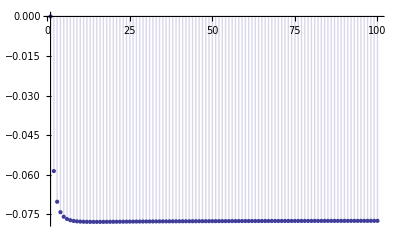

```mathematica
DiscretePlot[Re@zn2[n,1],{n,1,100}]
```

```mathematica
Zeta[.5]
```

```mathematica
zn2[1000000000.,1]
```

-0.0773539-1.60509×10^-18 ⅈ

```mathematica
-(-2)^(1+k) Gamma[1+k,0,-Log[√n]]-Log[n]^k/(2 √n)+∑_(j=2)^n Log[j]^k/(√j)/.k->1
```

-4 Gamma[2,0,-Log[√n]]-Log[n]/(2 √n)-1/4 (2 EulerGamma+π+Log[64]+2 Log[π]) Zeta[1/2]+Zeta^(1,0)[1/2,1+n]

```mathematica
N@Limit[-4 Gamma[2,0,-Log[√n]]-Log[n]/(2 √n)-1/4 (2 EulerGamma+π+Log[64]+2 Log[π]) Zeta[1/2]+Derivative[1,0][Zeta][1/2,1+n],n->Infinity]
```

Attributes::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in SuperscriptBox[.

Limit[3.92265-4. Gamma[2.,0.,-1. Log[√n]]-(0.5 Log[n])/(√n)+Zeta^(1,0)[0.5,1.+n],n→∞]

```mathematica
zn2[n,2]
```

8 Gamma[3,0,-Log[√n]]-Log[n]^2/(2 √n)+∑_(j=2)^n Log[j]^2/(√j)

```mathematica
zn2[1000000.,2]
```

-0.00835703+7.03468×10^-11 ⅈ

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
NLimit[zn2[n,1],n->Infinity]
```

-0.0773539-2.34499×10^-17 ⅈ

```mathematica
NLimit[zn2[n,2],n->Infinity]
```

-0.00835703+7.69864×10^-11 ⅈ

```mathematica
NLimit[zn2[n,3],n->Infinity]
```

0.00330975+3.42579×10^-9 ⅈ

```mathematica
NLimit[zn2[n,4],n->Infinity]
```

0.00287472+2.65881×10^-6 ⅈ

```mathematica
NLimit[zn2[n,5],n->Infinity]
```

0.00081609+7.31479×10^-6 ⅈ

```mathematica
NLimit[zn2[n,6],n->Infinity]
```

-0.000545871+5.5106×10^-6 ⅈ

```mathematica
NLimit[zn2[n,7],n->Infinity]
```

0.000575878+0.000119598 ⅈ

```mathematica
NLimit[zn2[n,8],n->Infinity]
```

0.0572435+0.00187555 ⅈ

```mathematica
NLimit[zn2[n,9],n->Infinity,WorkingPrecision->60]
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

```mathematica
NLimit[-1024 Gamma[10,0,-Log[√n]]-Log[n]^9/(2 √n)+∑_(j=2)^n Log[j]^9/(√j),n->∞,WorkingPrecision->60, Scale->.63]
```

0.450829256370052948579220565643530503911331+0. ⅈ

```mathematica
NLimit[zn2[n,10],n->Infinity]
```

20.8502+3.85348 ⅈ

```mathematica
NLimit[zn2[n,11],n->Infinity]
```

758.238+15.185 ⅈ

```mathematica
NLimit[zn2[n,12],n->Infinity]
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

NLimit[8192 Gamma[13,0,-Log[√n]]-Log[n]^12/(2 √n)+∑_(j=2)^n Log[j]^12/(√j),n→∞]

```mathematica
NLimit[zn2[n,13],n->Infinity]
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

NLimit[-16384 Gamma[14,0,-Log[√n]]-Log[n]^13/(2 √n)+∑_(j=2)^n Log[j]^13/(√j),n→∞]

```mathematica
NLimit[zn2[n,14],n->Infinity]
```

$Aborted

```mathematica
NLimit[zn2[n,15],n->Infinity]
```

```mathematica
NLimit[zn2[n,16],n->Infinity]
```

```mathematica
NLimit[zn2[n,17],n->Infinity]
```

```mathematica
NLimit[zn2[n,18],n->Infinity]
```

```mathematica
NLimit[zn2[n,19],n->Infinity]
```

```mathematica
NLimit[zn2[n,20],n->Infinity]
```

```mathematica
NLimit[zn2[n,21],n->Infinity]
```

```mathematica
NLimit[zn2[n,22],n->Infinity]
```

```mathematica
NLimit[zn2[n,23],n->Infinity]
```

```mathematica
NLimit[zn2[n,24],n->Infinity]
```

```mathematica
NLimit[zn2[n,25],n->Infinity]
```

```mathematica
NLimit[zn2[n,26],n->Infinity]
```

```mathematica
NLimit[zn2[n,27],n->Infinity]
```

```mathematica
NLimit[zn2[n,28],n->Infinity]
```

```mathematica
NLimit[zn2[n,29],n->Infinity]
```

```mathematica
NLimit[zn2[n,30],n->Infinity]
```

```mathematica
Sum[j^s,{j,1,n}]-Integrate[j^s,{j,0,n}]-n^s/2+Sum[BernoulliB[k]/k!D[n^s,{n,k-1}],{k,1,8}]
```

ConditionalExpression[-n^s+1/12 n^(-1+s) s-1/720 n^(-3+s) (-2+s) (-1+s) s+(n^(-5+s) (-4+s) (-3+s) (-2+s) (-1+s) s)/30240-(n^(-7+s) (-6+s) (-5+s) (-4+s) (-3+s) (-2+s) (-1+s) s)/1209600-n^(1+s)/(1+s)+HarmonicNumber[n,-s],Re[s]>-1]

```mathematica
zn2[n_,k_]:=-(-2)^(1+k) Gamma[1+k,0,-Log[√n]]-Log[n]^k/(2 √n)+∑_(j=2)^n Log[j]^k/(√j)
bo2[n_,t_]:=Sum[Log[j]^t/j^(1/2),{j,2,n}]-Integrate[Log[j]^t/j^(1/2),{j,1,n}]-Log[n]^t/n^(1/2)-Sum[BernoulliB[k]/k!D[Log[n]^t/n^(1/2),{n,k-1}],{k,1,10}]
bo3[n_,t_]:=Sum[Log[j]^t/j^(1/2),{j,2,n}]-((-2)^(1+t) Gamma[1+t,0,-Log[√n]])-Log[n]^t/n^(1/2)-Sum[BernoulliB[k]/k!D[Log[n]^t/n^(1/2),{n,k-1}],{k,1,10}]
```

```mathematica
N[bo3[n,1]/.n->1000000]
```

-0.0773539-3.72219×10^-17 ⅈ

```mathematica
-0.07735386079139062
```

```mathematica
-0.07735386079366435
-0.0773538607863884
```

```mathematica
zn2[100000.,3]
```

0.00330829+2.22842×10^-10 ⅈ

```mathematica
NLimit[zn2[n,3],n->Infinity]
```

0.00330975+3.42579×10^-9 ⅈ

```mathematica
NLimit[bo[n,3],n->Infinity]
```

0.00330878

```mathematica
NLimit[zn2[n,11],n->Infinity]
```

758.238+15.185 ⅈ

```mathematica
NLimit[bo[n,11],n->Infinity]
```

-456.194

```mathematica
N[bo2[n,11]/.n->10000]
```

0.00976563

```mathematica
N[bo2[n,8]/.n->100000]
```

-0.000354767

```mathematica
zn2[1000000,8.]
```

0.00805664+0.00130568 ⅈ

```mathematica
NLimit[zn2[n,2],n->Infinity]
```

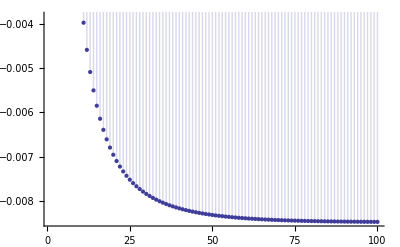

```mathematica
DiscretePlot[Re@zn2[n,2],{n,1,100}]
```

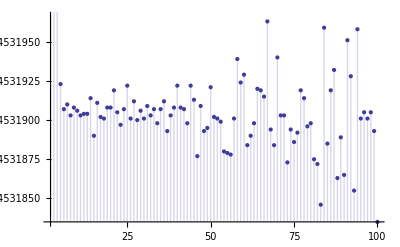

```mathematica
DiscretePlot[Re@bd[n],{n,2,100}]
```

```mathematica
FullSimplify@bo[n,2]
```

ConditionalExpression[1/(595137134592000 n^(25/2))(-16 (22670409511051+10920 n^2 (-607817345+352 n^2 (731043+40 n^2 (-12139+336 n^2 (43+120 n^2 (-1-96 n^(5/2)+96 n^3))))))+105 Log[n] (64 (32146869913+260 n^2 (-38797345+4224 n^2 (4269-3254 n^2+4928 n^4-26880 n^6-80640 n^7+645120 n^9)))-45045 (5133439+80 n^2 (-20995+8 n^2 (1287+32 n^2 (-33+8 n^2 (7+48 n^2 (1+4 n) (-1+8 n^2)))))) Log[n])+595137134592000 n^(25/2) ∑_(j=2)^n Log[j]^2/(√j)),Re[n]≥0||n∉Reals]

```mathematica
bb[n_]:=1/(595137134592000 n^(25/2))(-16 (22670409511051+10920 n^2 (-607817345+352 n^2 (731043+40 n^2 (-12139+336 n^2 (43+120 n^2 (-1-96 n^(5/2)+96 n^3))))))+105 Log[n] (64 (32146869913+260 n^2 (-38797345+4224 n^2 (4269-3254 n^2+4928 n^4-26880 n^6-80640 n^7+645120 n^9)))-45045 (5133439+80 n^2 (-20995+8 n^2 (1287+32 n^2 (-33+8 n^2 (7+48 n^2 (1+4 n) (-1+8 n^2)))))) Log[n])+595137134592000 n^(25/2) ∑_(j=2)^n Log[j]^2/(√j))
```

```mathematica
FullSimplify@bo2[n,2]
```

ConditionalExpression[1/(297568567296000 n^(23/2))(-8 (1871243360239+87360 n^2 (-7473495+22 n^2 (177331+320 n^2 (-475+756 (n^2-1280 n^(11/2)+1280 n^6)))))+105 Log[n] (4 (21925921301+208 n^2 (-39831725+264 n^2 (88069+160 n^2 (-563+56 n^2 (23+240 n^2 (-1+48 n^2))))))-45045 (223193+16 n^2 (-5525+8 n^2 (429+160 n^2 (-3+8 n^2 (1+4 n) (1-4 n+192 n^3))))) Log[n])+297568567296000 n^(23/2) ∑_(j=2)^n Log[j]^2/(√j)),Re[n]≥0||n∉Reals]

```mathematica
bc[n_]:=1/(297568567296000 n^(23/2))(-8 (1871243360239+87360 n^2 (-7473495+22 n^2 (177331+320 n^2 (-475+756 (n^2-1280 n^(11/2)+1280 n^6)))))+105 Log[n] (4 (21925921301+208 n^2 (-39831725+264 n^2 (88069+160 n^2 (-563+56 n^2 (23+240 n^2 (-1+48 n^2))))))-45045 (223193+16 n^2 (-5525+8 n^2 (429+160 n^2 (-3+8 n^2 (1+4 n) (1-4 n+192 n^3))))) Log[n])+297568567296000 n^(23/2) ∑_(j=2)^n Log[j]^2/(√j))
```

```mathematica
FullSimplify@bo2[n,3]
```

ConditionalExpression[1/(2425103265699861626880000 n^(39/2))(16 (32572022259617356906848633+1408 n^2 (-2546829381552005487765+133 n^2 (2620371801645139247+141440 n^2 (-3229899546685+4 n^2 (184827808649+2240 n^2 (-25713055+198 n^2 (57379+320 n^2 (-115+84 (n^2-11520 n^(11/2)+11520 n^6)))))))))+5 Log[n] (-8 (11884150070640380526438893+1408 n^2 (-971742778563097465585+399 n^2 (351548638800930241+2176 n^2 (-30074857160075+4 n^2 (1871243360239+87360 n^2 (-7473495+22 n^2 (177331+320 n^2 (-475+756 (n^2+1280 n^6)))))))))+3465 Log[n] (2 (3505722679891501697411+16 n^2 (-26112968662831984945+1064 n^2 (3689649641824737+1088 n^2 (-663023777675+8 n^2 (21925921301+208 n^2 (-39831725+264 n^2 (88069+160 n^2 (-563+56 n^2 (23+240 n^2 (-1+48 n^2))))))))))-4849845 (98185688640165+16 n^2 (-748306316175+56 n^2 (2062720845+64 n^2 (-6500375+8 n^2 (223193+16 n^2 (-5525+8 n^2 (429+160 n^2 (-3+8 n^2 (1+4 n) (1-4 n+192 n^3))))))))) Log[n]))+2425103265699861626880000 n^(39/2) ∑_(j=2)^n Log[j]^3/(√j)),Re[n]≥0||n∉Reals]

```mathematica
bd[n_]:=1/(2425103265699861626880000 n^(39/2))(16 (32572022259617356906848633+1408 n^2 (-2546829381552005487765+133 n^2 (2620371801645139247+141440 n^2 (-3229899546685+4 n^2 (184827808649+2240 n^2 (-25713055+198 n^2 (57379+320 n^2 (-115+84 (n^2-11520 n^(11/2)+11520 n^6)))))))))+5 Log[n] (-8 (11884150070640380526438893+1408 n^2 (-971742778563097465585+399 n^2 (351548638800930241+2176 n^2 (-30074857160075+4 n^2 (1871243360239+87360 n^2 (-7473495+22 n^2 (177331+320 n^2 (-475+756 (n^2+1280 n^6)))))))))+3465 Log[n] (2 (3505722679891501697411+16 n^2 (-26112968662831984945+1064 n^2 (3689649641824737+1088 n^2 (-663023777675+8 n^2 (21925921301+208 n^2 (-39831725+264 n^2 (88069+160 n^2 (-563+56 n^2 (23+240 n^2 (-1+48 n^2))))))))))-4849845 (98185688640165+16 n^2 (-748306316175+56 n^2 (2062720845+64 n^2 (-6500375+8 n^2 (223193+16 n^2 (-5525+8 n^2 (429+160 n^2 (-3+8 n^2 (1+4 n) (1-4 n+192 n^3))))))))) Log[n]))+2425103265699861626880000 n^(39/2) ∑_(j=2)^n Log[j]^3/(√j))
```

```mathematica
E^-0.0773538607863884
```

0.925562

```mathematica
bo2[n,1]
```

ConditionalExpression[-4-2 √n (-2+Log[n])-Log[n]/(2 √n)+(-71697105/(256 n^(19/2))+(34459425 Log[n])/(512 n^(19/2)))/47900160+(264207/(64 n^(15/2))-(135135 Log[n])/(128 n^(15/2)))/1209600+(-1689/(16 n^(11/2))+(945 Log[n])/(32 n^(11/2)))/30240+1/720 (23/(4 n^(7/2))-(15 Log[n])/(8 n^(7/2)))+1/12 (-1/n^(3/2)+Log[n]/(2 n^(3/2)))-1/4 (2 EulerGamma+π+Log[64]+2 Log[π]) Zeta[1/2]+Zeta^(1,0)[1/2,1+n],Re[n]≥0||n∉Reals]

```mathematica
(1/2- s)(1-((2 ⅈ)/(ⅈ-2 s/I))+ Sum[(s)^k/k!bbo3[n,k],{k,0,l}])/.s->s-1/2
```

```mathematica
(1-s) (1-1/s+∑_(k=0)^l ((-1/2+s)^k bbo3[n,k])/(k!))
```

```mathematica
bo3[n_,t_]:=Sum[Log[j]^t/j^(1/2),{j,2,n}]-((-2)^(1+t) Gamma[1+t,0,-Log[√n]])-Log[n]^t/n^(1/2)-Sum[BernoulliB[k]/k!D[Log[n2]^t/n^(1/2),{n2,k-1}]/.n2->n,{k,1,10}]
s15a[n_,s_, l_]:=1-1/(1-s)+ Sum[(1/2-s)^k/k!bo3[n,k],{k,0,l}]
```

```mathematica
s15a[10,.500001,200]
```

-1.46168-1.44844×10^-21 ⅈ

```mathematica
Zeta[s]/.s->.500001
```

-1.46036

```mathematica
FullSimplify[Integrate[( Log[j] )^k/j^(1/2),{j,0,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) Gamma[1+k,-Log[n]/2],k>-1]

```mathematica
FullSimplify[Integrate[( Log[j] )^k/j^(1/2),{j,1,n}],Element[k,Integers]]
```

ConditionalExpression[(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2]),k≥0&&Log[n]>0]

```mathematica
(-1)^k 2^(1+k) (-k!+Gamma[1+k,-Log[n]/2])/.n->100./.k->3
```

754.862-3.69776×10^-13 ⅈ

```mathematica
(-1)^(k+1) 2^(1+k) (Gamma[1+k,0,-Log[n]/2])/.n->100./.k->2
```

199.738-7.33826×10^-14 ⅈ

```mathematica
(-2)^(1+k) (Gamma[1+k,0,-Log[n]/2])/.n->100./.k->3
```

754.862-3.69776×10^-13 ⅈ

```mathematica
(-2)^(1+k) (Gamma[1+k,0,Log[1/n^(1/2)]])/.n->100./.k->3
```

754.862-3.69776×10^-13 ⅈ

```mathematica
br[k_]:=D[Zeta[1/2-s]-1+1/(1/2+s),{s,k}]/.s->0
```

```mathematica
Table[{k,N[FullSimplify[br[k]]]},{k,0,20}]//TableForm
```

0 | -0.460355
1 | -0.0773539
2 | -0.00835701
3 | 0.00330925
4 | 0.00268028
5 | 0.000600662
6 | -0.000546537
7 | -0.000702627
8 | -0.000337601
9 | 0.000105381
10 | 0.000360489
11 | 0.000335693
12 | 0.
13 | 0.
14 | 0.
15 | 0.
16 | 0.
17 | 0.
18 | 0.
19 | 0.
20 | 0.

```mathematica
bo4[k_]:=D[Zeta[1/2-s]-1+1/(1/2+ s),{s,k}]/.s->0
s16[s_, l_]:=1-1/(1/2+s)+ Sum[s^k/k!bo4[k],{k,0,l}]
s17[s_]:=1-(1/(1/2-s))+ Sum[s^k/k!bo4[k],{k,0,Infinity}]
```

```mathematica
$MaxExtraPrecision=500
```

500

```mathematica
N[s16[1/10+16I,70],100]
```

0.921881997000873024345167733002211409445956630456769083747863413401100357201826816521769431551351908-1.323651192706184466871100858111552042914076142899828421953946052997015908679896303371831077097092885 ⅈ

```mathematica
Zeta[.5-(.1+16I)]
```

0.921882-1.32365 ⅈ

```mathematica
N[s16[Im@ZetaZero@1 I,100],120]
```

-8.5939786072054024919539719592717108795005717843121713438372869531696345259933533383418468489991143894492978041722095511×10^-27+4.12915899521356031566857018354641219064324847269524558357155370186552060978096579510509414645337584626725585827502962179×10^-26 ⅈ

```mathematica
Zeta[.5-(30I)]
```

-0.120642+0.583691 ⅈ

```mathematica
Integrate[x^z/x^(1/2),{x,0,1}]
```

ConditionalExpression[2/(1+2 z),Re[z]>-1/2]

```mathematica
sa1[n_,s_]:=Sum[j^s/j^(1/2),{j,1,n}]-Integrate[j^s/j^(1/2),{j,0,n}]
sa2[n_,s_]:=1-1/(1/2+s)+Sum[j^s/j^(1/2),{j,2,n}]-Integrate[j^s/j^(1/2),{j,1,n}]
```

```mathematica
sa2[100000., .2]
```

-0.888745

```mathematica
Zeta[.5 - .2]
```

-0.904559

```mathematica
sa1[100000., .2]
```

-0.886481

```mathematica
Integrate[j^s/j^(1/2),{j,0,1}]
```

ConditionalExpression[2/(1+2 s),Re[s]>-1/2]

```mathematica
N[1-1/(1/2+s)/.s->Im@ZetaZero@1 I]
```

0.997501+0.0706593 ⅈ

```mathematica
Integrate[Cos[s I Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[2/(1-4 s^2),-1/2<s<1/2]

```mathematica
Integrate[Sin[(s) Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[-(4 s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[Sin[s Log[x]+ArcTan[2s]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
bo4[k_]:=D[Zeta[1/2-s]-1+1/(1/2+ s),{s,k}]/.s->0
ex[s_, l_]:=1-1/(1/2+s)+ Sum[s^k/k!bo4[k],{k,0,l}]
cs[s_, l_]:=1-2/(1+4 s^2)+ Sum[(-1)^k s^(2k)/((2k)!)bo4[2k],{k,0,Floor[l/2]}]
sn[s_, l_]:=(4 s)/(1+4 s^2)+ Sum[(-1)^k s^(2k+1)/((2k+1)!)bo4[2k+1],{k,0,Floor[l/2]}]
exr[s_]:=Zeta[1/2-s]
csr[s_]:=(Zeta[1/2-s I ]+Zeta[1/2+s I ])/2
snr[s_]:=(Zeta[1/2-s I]-Zeta[1/2+s I ])/(2 I)
exd[s_]:=Zeta[1/2-s]-(1-1/(1/2+s))
csd[s_]:=(Zeta[1/2-s I ]+Zeta[1/2+s I ])/2-(1-2/(1+4 s^2))
snd[s_]:=(Zeta[1/2-s I]-Zeta[1/2+s I ])/(2 I)-((4 s)/(1+4 s^2))
```

```mathematica
N[sn[14,100],100]
```

0.1032581232664500579023630952954409749087096055462790296425727172916244189547968076883762335440600151

```mathematica
snr[14.]
```

0.103258+0. ⅈ

```mathematica
FullSimplify[(4 ⅈ s)/(-1+4 s^2)]
```

(4 ⅈ s)/(-1+4 s^2)

```mathematica
N[sn[Im@ZetaZero@1,100],100]
```

-6.946237152308122659517809705439632597840669471264057813581403415601836286424215377891136460505849031×10^-28

```mathematica
N[cs[Im@ZetaZero@1,100],100]
```

-8.593978607205402491953971959271710879500571784312171343837286953169634525993353338341846848999114389×10^-27

```mathematica
N[ex[5/2,50],50]
```

7.1503225982775753754183080074996625489028301530513×10^-44

```mathematica
exa[s_, l_]:= Sum[s^k/k!bo4[k],{k,0,l}]
exa2[s_, l_]:= Table[s^k/k!bo4[k],{k,0,l}]
sna[s_, l_]:= Sum[(-1)^k s^(2k+1)/((2k+1)!)bo4[2k+1],{k,0,Floor[l/2]}]
csa[s_, l_]:= Sum[(-1)^k s^(2k)/((2k)!)bo4[2k],{k,0,Floor[l/2]}]
tana[s_, l_]:= Sum[(D[Tan[x],{x,k}]/.x->0) s^k/(k!)bo4[k],{k,0,l}]
```

```mathematica
tana[2.5,30]
```

-0.111743

```mathematica
1-1/(1/2+(3.5))
```

0.75

```mathematica
-7./12
```

-0.583333

```mathematica
Zeta[-3]-3/4
```

-89/120

```mathematica
Expand@FullSimplify[snd[1]]
```

-4/5-1/2 ⅈ Zeta[1/2-ⅈ]+1/2 ⅈ Zeta[1/2+ⅈ]

```mathematica
Table[D[Tan[x],{x,k}]/.x->0,{k,0,10}]
```

{0,1,0,2,0,16,0,272,0,7936,0}

```mathematica
snt[s_, l_]:=Flatten[{N[(4 s)/(1+4 s^2)],Table[N[(-1)^k s^(2k+1)/((2k+1)!)bo4[2k+1],70],{k,0,Floor[l/2]}]}]//TableForm
sant[s_, l_]:=Table[N[s^(2k+1),70],{k,0,Floor[l/2]}]//TableForm
sant2[s_, l_]:=Table[N[(-1)^k bo4[2k+1]/((2k+1)!),70],{k,0,Floor[l/2]}]//TableForm
```

```mathematica
snt[Im@ZetaZero@1,100]
```

```mathematica
snt[Im@ZetaZero@1+(1/20)I,100]
```

```mathematica
sant2[Im@ZetaZero@1+(1/20)I,100]
```

```mathematica
sot[s_, k_]:=N[(-1)^k s^(2k+1)/((2k+1)!)bo4[2k+1],70]
```

```mathematica
Series[Sin[x+a],{x,0,10}]
```

Sin[a]+Cos[a] x-1/2 Sin[a] x^2-1/6 Cos[a] x^3+1/24 Sin[a] x^4+1/120 Cos[a] x^5-1/720 Sin[a] x^6-(Cos[a] x^7)/5040+(Sin[a] x^8)/40320+(Cos[a] x^9)/362880-(Sin[a] x^10)/3628800+O[x]^11

```mathematica
Table[Sin[a-k Pi/2],{k,0,10}]/.a->0
```

{0,-1,0,1,0,-1,0,1,0,-1,0}

```mathematica
Sin[ArcTan[2s]]
```

(2 s)/(√(1+4 s^2))

```mathematica
Cos[ArcTan[2s]]
```

1/(√(1+4 s^2))

```mathematica
Integrate[Cos[s Log[x]+a]/x^(1/2),{x,0,1}]
```

(2 (Cos[a]+2 s Sin[a]))/(1+4 s^2)

```mathematica
bo4[k_]:=D[Zeta[1/2-s]-1+1/(1/2+ s),{s,k}]/.s->0
ex[s_, l_]:=1-1/(1/2+s)+ Sum[s^k/k!bo4[k],{k,0,l}]
cs[s_, l_]:=1-2/(1+4 s^2)+ Sum[(-1)^k s^(2k)/((2k)!)bo4[2k],{k,0,Floor[l/2]}]
sn[s_, l_]:=(4 s)/(1+4 s^2)+ Sum[(-1)^k s^(2k+1)/((2k+1)!)bo4[2k+1],{k,0,Floor[l/2]}]
asn[s_, l_,a_]:=Cos[a]-(2 (Cos[a]+2 s Sin[a]))/(1+4 s^2)+ Sum[Cos[a+k Pi/2] s^k/(k!)bo4[k],{k,0,l}]
arcn[s_, l_]:=1/(√(1+4 s^2))+ Sum[Sin[ArcTan[2s]+k Pi/2] s^k/(k!)bo4[k],{k,0,l}]
exr[s_]:=Zeta[1/2-s]
csr[s_]:=(Zeta[1/2-s I ]+Zeta[1/2+s I ])/2
snr[s_]:=(Zeta[1/2-s I]-Zeta[1/2+s I ])/(2 I)
```

```mathematica
Cos[s Log[1]+a]/1^(1/2)
```

Cos[a]

```mathematica
asn[3.,30,.3I]
```

0.55689-0.0240256 ⅈ

```mathematica
Cos[.3I]cs[3.,30]-Sin[.3I]sn[3.,30]
```

0.55689-0.0240256 ⅈ

```mathematica
Sin[a]-(-s Cos[a]+Sin[a])/(1+s^2)/.a->0
```

s/(1+s^2)

```mathematica
FullSimplify[Sin[a]-(2 (-2 s Cos[a]+Sin[a]))/(1+4 s^2)/.a->-ArcTan[1/(4 s)-s]-Pi/2]
```

0

```mathematica
arcnt[s_, l_]:=Flatten[{Table[Sin[ArcTan[(4s^2-1)/(4s)]+k Pi/2] s^k/(k!)bo4[k],{k,0,l}]}]//TableForm
```

```mathematica
N[arcnt[Im@ZetaZero@1,70],100]
```

-0.4592038552850402002687492390332820849046744214246302173817348967944218203219523173774388242432505445
-0.07725718801926356635000175019962703072442585624875764194661195335378185603848839431169393971748190173
0.8327391644804705999532009861380395336657508853464738364519636861893134809336217691689677932256583293
-0.1100548916748698815728444063269818679201009731517266718726880389320884749522869485325748612735663251
4.446634642551341343362100479645044164478747284793012494136546063906484410935561568253409874834864198
0.1995516547110514459020373419972482472254381774485456799783714516442298729428602023710149131522418146
6.038440176492559057018325828087032104504276481161551994803611270733797977318775013718169426298155533
1.110389033455212981659164708302292503352132292968548415529529981496618840163424321981422406060982133
-13.30749615442252718585032197502830401724958524814392134943485924654711638770017278278660139404672386
0.462190906973066341619011355014596210152281799862714317751472468053010835182117316390114823426448739
-31.5133107705270570031762470950266199618367917230553601509803881304047951068990785959778579082397811
-2.749769760552608452629309442553233472197554329882511846857422651252387100187995236424207187425244325
16.02259840826341379503880964307291660400202252438902108464974516347299423117010431879331809308223732
-1.749422839682394592603480027008434148249090210193464432410958814503461489982299116014633515230819846
54.43557855571860097222454220573346425264853183236133736400016321598259875277432659422438367126785675
3.612024294787249569682115570729974669865186587223761358997731891283432893612108481675989819712482933
-16.51057465199657890021728549127601961581514651029056692909806994550528910449631545729816251421712628
1.801527874167000540056384084465919582811345905693601466344589780613245059979287535216397871281127488
-48.82490934923273066851221992838483024411417081350882651130963860418759045472856039722412831767280874
-3.060183808761694795606172705575763202250202989111636356450790491250234692489063480151572657173613371
17.47245170709799448859694914468007122261715959251077579369756660248111439412812359522524184823375231
-0.7081533286370554301727823345543156752861693326335436813216115454269394662659720759027408890547057691
24.825777372696508466384773979272952838374960366419452847101788834353249621015134319566824886338213
1.680013649007403576919461744299292850875249264925017018235321226119118890051805617337983738999473156
-12.6974980714496733529043437661207104418124158885131079952335880844947455186284230310787989902587852
-0.04120454930042027684811530718128574804027468682091021251155166248410045154907798866577608547844538091
-6.707859506759736280210638522922118970789932893448834554187034130066283382395570026806768910227018916
-0.5667397473274569300047490762547441396828811538507125311526191121297863346925254528460743324120142432
5.437552658937060250179640534314805607691941624451511986960992224824627344803802209889615803051745674
0.1375883654931820226447644732502563604459252010985966282538945554338703236741352798458434715403418562
0.5444218702259487053474475129970875811059970595686444878273671791040378981749149011604840924854646066
0.1061640945293212845431618863950606751614195571026455791932981639109663284887180616059227156138419649
-1.339100520848578889521258020571081843362705292686967187195193885867882372738418814873589481169262517
-0.05260596016783529476570620553311486896179671921422802711711134227620579818506408535418609708981160049
0.2004617385985818175877574012168718510532065366385128583733259663418177790235957398870950959100653123
-0.006932029728944249565556982149449564600338962418999014612631649360921789619463823284286731297686452299
0.1761059463389465462590546947193698968302916141952190184509924427650702335892762994157403220174614708
0.009664504624255372086232776165521584656346424348874092539253914010224835489894450048245054265969647383
-0.06818409888716468560327310426144944699051568278497708047133076518791669384239518143625960555229129248
-0.001212138356965194490473938925410072569841655612413968858702902082370563872182582004493347774666289493
-0.00716096388160430154379922634801083358138421467877042103827535591688119378920135190244411663157053248
-0.0008760000687386449278133738677729665137713179773501103591540810570223868553827590478765099241269515608
0.009099405779673962875383610770887242808518727019638454379505707723642320607156963537556378860016475831
0.0003134872992824968868905216317470778036748199841021703646643800413504597105762081331151509552527944108
-0.001222587352877254285647648756512473887600447475759786912721323593131394024978311259979941036392442286
0.00001535234484187252695882236268135874242086662131318202899189440407870950501116444325629352682260962226
-0.0005403319803425579224553054967486419416332976058249978273110128170274734429530909325778637298592912801
-0.00002895110259897659040219354102399922892015204235570597257318855065127008301805104822599219732727798309
0.0002043447771771558490044381290786370216823735006467306901989070497856059857639440663967201419301454358
4.646346364258451910113949996279734588476852849593496991474150076278104536937272460895942628078641872×10^-6
-2.547476397628985329891202446142113147716752101875459228075953646782736887357139106082701850341317662×10^-6
1.01306323801731880175430247188234810711101239172558778544967000440875307047743755870589190556833013×10^-6
-0.0000123600970581494832540860252223207486976631648832468204819889588301932801877310141014228856659677241
-4.699521140991757464327104091778013644702233223527282659507216508987008364202396902063955655499344027×10^-7
2.461593735824100158847135073863651371844013668818416294454984017804026128217146794401100916436310555×10^-6
3.217852306010126005058592813163025410082314942040255969007240795305859232141504219410824992221596266×10^-8
1.87049751278648398090633418460418124779836447610218473268610740516916667320432910869885525896822992×10^-7
1.727697361244746296980207365765264243491789347768871129719759864316937648585738690689124194657978369×10^-8
-1.486389091806213221263840951638552737791953829068139148825091428561228770737513119823380087542150884×10^-7
-4.475935944177638663364139897998271212350604752106326683551110601426736004816236181837695658832599021×10^-9
1.779446143999432297070653648764516264230563956912134978117323795143063938340071917376333273764609851×10^-8
6.068048915574869853103228786505923732187273179321916155957607462949680267449976824850109173156717465×10^-11
2.801505955902452657194889294592359116913717609106921150826575662667164542769955100706169659673497792×10^-9
1.573583501348536285328464656950525311486745559727997997822361867795923533807868160889043275371862548×10^-10
-1.099444831189142337816962360226105608662935040609794603788345357172062477059025079462429970679548979×10^-9
-2.76834161423900382287945901886250781399654103209548230370952552369454493245560406636318046193127553×10^-11
8.427867225711825449784305626583227655166855252677289407332070250506463295966066666463829928251055616×10^-11
-5.85187228386375604371716504502956998410757065548210579895529315348586864691703427109846242670013882×10^-13
2.017861454314875658598529645812689065306176266368760096169745736422129810377948665505579520575874312×10^-11
8.977570810929938875273405344669967781126955448866070040491552284752149411041590429737450715925561204×10^-13
-5.442912455867807416802509466521935611712315857897238886174761195887399574377317769671869293192867524×10^-12

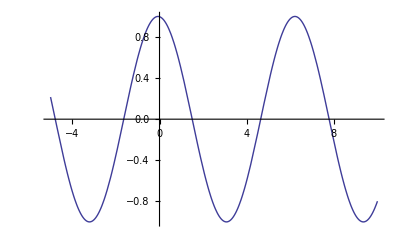

```mathematica
Plot[((-1+4s^2)Cos[a]- 4 s Sin[a])/(1+4 s^2)/.s->Im@ZetaZero@1,{a,-5,10}]
```

```mathematica
FullSimplify[((-1+4s^2)Cos[a]- 4 s Sin[a])/(1+4 s^2)/.a->ArcTan[(4s^2-1)/(4s)]]
```

0

```mathematica
FullSimplify[ArcTan[(4s^2-1)/(4s)]]
```

-ArcTan[1/(4 s)-s]

```mathematica
N[-ArcTan[1/(4 s)-s]/.s->Im@ZetaZero@4]
```

1.53793

```mathematica
FullSimplify[Cos[ArcTan[(4s^2-1)/(4s)]]]
```

4/(√(8+1/s^2+16 s^2))

```mathematica
ArcTan[(4s^2-1)/(4s)]/.s->Im@ZetaZero@1
```

ArcTan[(-1+4 Im[ZetaZero[1]]^2)/(4 Im[ZetaZero[1]])]

```mathematica
N[asn[Im@ZetaZero@1,100,ArcTan[(-1+4 Im[ZetaZero[1]]^2)/(4 Im[ZetaZero[1]])]],100]
```

-4.179562665108838089132409139029642903052600710212906648929145901346607494665256532240334183868042705×10^-26

```mathematica
FullSimplify@Expand[(-1/2+z)/(1/2+z)]
```

1-2/(1+2 z)

```mathematica
FullSimplify@Expand[-(1-4 z^2)/(1+4 z^2)]
```

1-2/(1+4 z^2)

```mathematica
(1-2z)(1+2z)/((1-2z I)(1+2z I))
```

((1-2 z) (1+2 z))/((1-2 ⅈ z) (1+2 ⅈ z))

```mathematica
-(1-4 z^2)/(1+4 z^2)
```

(-1+4 z^2)/(1+4 z^2)

```mathematica
bo4[k_]:=D[Zeta[1/2-s]-1+1/(1/2+ s),{s,k}]/.s->0
```

```mathematica
N[(bo4[1]+2bo4[0]-2)/(1+bo4[0])]
```

-5.55562

```mathematica
Sum[1/N[Im@ZetaZero@k]I+1/N[Im@ZetaZero@-k I],{k,1,20}]
```

0.+0.982304 ⅈ

```mathematica
N[Sum[1/Im@ZetaZero@k+1/Im@ZetaZero@k,{k,1,2000}]]
```

5.68099

```mathematica
N[1/Im@ZetaZero@2001]I
```

0.+0.000397366 ⅈ

```mathematica
Sum[1/(I N[Im@ZetaZero@k])+1/(N[Im@ZetaZero@-k] I),{k,1,20}]
```

0.+0. ⅈ

```mathematica
bo4[k_]:=D[Zeta[1/2-s]-1+1/(1/2+ s),{s,k}]/.s->0
ex[s_, l_]:=1-1/(1/2+s)+ Sum[s^k/k!bo4[k],{k,0,l}]
ex2[s_, l_]:=(1/(1+2s))((-1+2s)+ Sum[(1+2s)s^k/k!bo4[k],{k,0,l}])
ex3[s_, l_]:=(1/(1+2s))(-1+2s+ Sum[s^k/k!bo4[k]+2s^(k+1)/k!bo4[k],{k,0,l}])
ex4[s_, l_]:=(1/(1+2s))(-1+2s+ Sum[s^k/k!bo4[k],{k,0,l}]+ 2Sum[s^k/(k-1)!bo4[(k-1)],{k,1,l+1}])
ex5[s_, l_]:=(1/(1+2s))(-1+2s+ bo4[0]+Sum[s^k/k!bo4[k],{k,1,l}]+ 2Sum[s^k/(k-1)!bo4[(k-1)],{k,1,l+1}])
ex6[s_, l_]:=(1/(1+2s))(-1+2s+ bo4[0]+Sum[s^k/k!bo4[k],{k,1,l}]+ 2Sum[s^k/(k-1)!bo4[(k-1)],{k,1,l}]+2s^(l+1)/l!bo4[l])
ex7[s_, l_]:=(1/(1+2s))(-1+2s+ bo4[0]+Sum[(1/k!bo4[k])s^k,{k,1,l}]+ Sum[(2/(k-1)!bo4[(k-1)])s^k,{k,1,l}]+2s^(l+1)/l!bo4[l])
ex8[s_, l_]:=(1/(1+2s))(-1+2s+ bo4[0]+Sum[((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))s^k,{k,1,l}]+2s^(l+1)/l!bo4[l])
ex9[s_, l_]:=(1/(1+2s))(-1+ bo4[0])(1+(2s+Sum[((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))s^k,{k,1,l}]+2s^(l+1)/l!bo4[l])/(-1+ bo4[0]))
ex9a[s_, l_]:=(1+(2s+Sum[((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))s^k,{k,1,l}]+2s^(l+1)/l!bo4[l])/(-1+ bo4[0]))
ex9b[s_, l_]:=(1+((2+bo4[1]+2bo4[0])s+Sum[((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))s^k,{k,2,l}]+2s^(l+1)/l!bo4[l])/(-1+ bo4[0]))
ex9c[s_, l_]:=1+(2+bo4[1]+2bo4[0])/(-1+ bo4[0])s+(Sum[((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))s^k,{k,2,l}]+2s^(l+1)/l!bo4[l])/(-1+ bo4[0])
ex9d[s_, l_]:=1+(2-Zeta'[1/2]/Zeta[1/2])s+(Sum[((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))s^k,{k,2,l}]+2s^(l+1)/l!bo4[l])/(-1+ bo4[0])
ex9e[s_, l_]:=1+(2-Zeta'[1/2]/Zeta[1/2])s+(Sum[((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))/(-1+ bo4[0])s^k,{k,2,l}]+2s^(l+1)/l!bo4[l]/(-1+ bo4[0]))
ex9f[s_, l_]:=1+(2-Zeta'[1/2]/Zeta[1/2])s+(Sum[((-1)^k (-2k (D[Zeta[r],{r,k-1}]/.r->1/2)+(D[Zeta[r],{r,k}]/.r->1/2))/(k!)/Zeta[1/2])s^k,{k,2,l}]+2s^(l+1)/l!bo4[l]/(-1+ bo4[0]))
ex10[s_, l_]:=Zeta[1/2]/(1+2 s)ex9f[s,l]



spow1[s_]:=(2+bo4[1]+2bo4[0])/(-1+ bo4[0])
```

```mathematica
N@ex9f[z,50]
```

1.-0.686092 z+0.1088 z^2+0.00534492 z^3-0.000831825 z^4-0.000156374 z^5-6.33542×10^-6 z^6+1.13505×10^-6 z^7+1.9666×10^-7 z^8+1.12683×10^-8 z^9-4.65739×10^-10 z^10-1.41875×10^-10 z^11-1.11685×10^-11 z^12+4.24249×10^-8 z^28+4.12363×10^-7 z^31+3.01076×10^-6 z^34-0.000467447 z^41+0.00308412 z^44+0.0122054 z^46

```mathematica
ex10[.3,70]
```

-0.733921

```mathematica
Zeta[.5-.3]
```

-0.733921

```mathematica
Expand[1-1/(1/2+s)]/.s->.2+.3I
```

-0.206897+0.517241 ⅈ

```mathematica
1-1/(1/2+s)
```

```mathematica
Expand[(-1+2s)/(1+2s)]/.s->.2+.3I
```

-0.206897+0.517241 ⅈ

```mathematica
FullSimplify@spow1[z]
```

2-Zeta'[1/2]/Zeta[1/2]

```mathematica
N[ex9[Im@ZetaZero@1 I,70],70]
```

-3.59151909086676140375516758442929546720724674475899117564541697625077×10^-13+1.717168032339678214985062948237644543463127022775810879118152015848094×10^-12 ⅈ

```mathematica
N[ex9b[Im@ZetaZero@1 I,70],70]
```

3.348676498252417461613789760803280989135997098774009358580974791546566×10^-11+5.77658298372752714622515174035887786398023700606782499857845859152283×10^-12 ⅈ

```mathematica
N[ex9b[-1/2,70],70]
```

1.36953047217987304619108670264162760211820401743103104843286345727002

```mathematica
FullSimplify[(2+bo4[1]+2bo4[0])/(-1+ bo4[0])]
```

```mathematica
2-Zeta'[1/2]/Zeta[1/2]
```

```mathematica
FullSimplify[((1/2!bo4[2])+(2/(2-1)!bo4[(2-1)]))/(-1+ bo4[0])]
```

(-4 Zeta'[1/2]+Zeta''[1/2])/(2 Zeta[1/2])

```mathematica
((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))/(-1+ bo4[0])
```

```mathematica
bk[k_]:=((1/k!bo4[k])+(2/(k-1)!bo4[(k-1)]))/(-1+ bo4[0])
```

```mathematica
Table[FullSimplify[bk[k]],{k,2,10}]
```

{(-4 Zeta'[1/2]+Zeta''[1/2])/(2 Zeta[1/2]),-(-6 Zeta''[1/2]+Zeta^(3)[1/2])/(6 Zeta[1/2]),(-8 Zeta^(3)[1/2]+Zeta^(4)[1/2])/(24 Zeta[1/2]),-(-10 Zeta^(4)[1/2]+Zeta^(5)[1/2])/(120 Zeta[1/2]),(-12 Zeta^(5)[1/2]+Zeta^(6)[1/2])/(720 Zeta[1/2]),-(-14 Zeta^(6)[1/2]+Zeta^(7)[1/2])/(5040 Zeta[1/2]),(-16 Zeta^(7)[1/2]+Zeta^(8)[1/2])/(40320 Zeta[1/2]),-(-18 Zeta^(8)[1/2]+Zeta^(9)[1/2])/(362880 Zeta[1/2]),(-20 Zeta^(9)[1/2]+Zeta^(10)[1/2])/(3628800 Zeta[1/2])}

```mathematica
FullSimplify[(1/(1+2s))(-1+ bo4[0])]
```

Zeta[1/2]/(1+2 s)

```mathematica
Table[(-1)^k (-2k (D[Zeta[s],{s,k-1}]/.s->1/2)+(D[Zeta[s],{s,k}]/.s->1/2))/(k!)/Zeta[1/2],{k,2,10}]
```

{(-4 Zeta'[1/2]+Zeta''[1/2])/(2 Zeta[1/2]),-(-6 Zeta''[1/2]+Zeta^(3)[1/2])/(6 Zeta[1/2]),(-8 Zeta^(3)[1/2]+Zeta^(4)[1/2])/(24 Zeta[1/2]),-(-10 Zeta^(4)[1/2]+Zeta^(5)[1/2])/(120 Zeta[1/2]),(-12 Zeta^(5)[1/2]+Zeta^(6)[1/2])/(720 Zeta[1/2]),-(-14 Zeta^(6)[1/2]+Zeta^(7)[1/2])/(5040 Zeta[1/2]),(-16 Zeta^(7)[1/2]+Zeta^(8)[1/2])/(40320 Zeta[1/2]),-(-18 Zeta^(8)[1/2]+Zeta^(9)[1/2])/(362880 Zeta[1/2]),(-20 Zeta^(9)[1/2]+Zeta^(10)[1/2])/(3628800 Zeta[1/2])}

```mathematica
ex9f[s_, l_]:=1+(2-Zeta'[1/2]/Zeta[1/2])s+(Sum[((-1)^k (-2k (D[Zeta[r],{r,k-1}]/.r->1/2)+(D[Zeta[r],{r,k}]/.r->1/2))/(k!)/Zeta[1/2])s^k,{k,2,l}]+2s^(l+1)/l!bo4[l]/(-1+ bo4[0]))
roots[n_]:=If[(c=Exponent[f=N[ex9f[z,100],100],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
```

```mathematica
roots[10]
```

```mathematica
N[ex9f[z,100],100]
```

```mathematica
FullSimplify[(1/(1+2s))(-1+ bo4[0])]
```

Zeta[1/2]/(1+2 s)

```mathematica
ex9f[s_, l_]:=1+(2-Zeta'[1/2]/Zeta[1/2])s+Sum[((-1)^k (-2k (D[Zeta[r],{r,k-1}]/.r->1/2)+(D[Zeta[r],{r,k}]/.r->1/2))/(k!)/Zeta[1/2])s^k,{k,2,l}]

ex9g[s_, l_]:=1+Sum[((-1)^k (-2k (D[Zeta[r],{r,k-1}]/.r->1/2)+(D[Zeta[r],{r,k}]/.r->1/2))/(k!)/Zeta[1/2])s^k,{k,1,l}]
ex10[s_, l_]:=Zeta[1/2]/(1+2 s)ex9g[s,l]
```

```mathematica
ex10[.4+.1I,50]
```

-0.589453+0.11391 ⅈ

```mathematica
Zeta[.5-(.4+.1I)]
```

-0.589453+0.11391 ⅈ

```mathematica
Table[FullSimplify[((-1)^k (-2k (D[Zeta[r],{r,k-1}]/.r->1/2)+(D[Zeta[r],{r,k}]/.r->1/2))/(k!)/Zeta[1/2])]s^k,{k,1,10}]
```

{s (2-Zeta'[1/2]/Zeta[1/2]),(s^2 (-4 Zeta'[1/2]+Zeta''[1/2]))/(2 Zeta[1/2]),-(s^3 (-6 Zeta''[1/2]+Zeta^(3)[1/2]))/(6 Zeta[1/2]),(s^4 (-8 Zeta^(3)[1/2]+Zeta^(4)[1/2]))/(24 Zeta[1/2]),-(s^5 (-10 Zeta^(4)[1/2]+Zeta^(5)[1/2]))/(120 Zeta[1/2]),(s^6 (-12 Zeta^(5)[1/2]+Zeta^(6)[1/2]))/(720 Zeta[1/2]),-(s^7 (-14 Zeta^(6)[1/2]+Zeta^(7)[1/2]))/(5040 Zeta[1/2]),(s^8 (-16 Zeta^(7)[1/2]+Zeta^(8)[1/2]))/(40320 Zeta[1/2]),-(s^9 (-18 Zeta^(8)[1/2]+Zeta^(9)[1/2]))/(362880 Zeta[1/2]),(s^10 (-20 Zeta^(9)[1/2]+Zeta^(10)[1/2]))/(3628800 Zeta[1/2])}

```mathematica
FullSimplify[((-1)^k (-2k (D[Zeta[r],{r,k-1}]/.r->1/2)+(D[Zeta[r],{r,k}]/.r->1/2))/(k!)/Zeta[1/2])]
```

((-1)^k (-2 k Zeta^(-1+k)[1/2]+Zeta^(k)[1/2]))/(k! Zeta[1/2])

```mathematica
big[N@Im@ZetaZero@1I]
```

-2.76898×10^-13-3.66901×10^-13 ⅈ

```mathematica
N[Im@ZetaZero@1,100]
```

14.13472514173469379045725198356247027078425711569924317568556746014996342980925676494901039317156101

```mathematica
14.134725141734695
```

14.1347

```mathematica
ex9f[s_, l_]:=1+(2-Zeta'[1/2]/Zeta[1/2])s+(Sum[((-1)^k (-2k (D[Zeta[r],{r,k-1}]/.r->1/2)+(D[Zeta[r],{r,k}]/.r->1/2))/(k!)/Zeta[1/2])s^k,{k,2,l}]+2s^(l+1)/l!bo4[l]/(-1+ bo4[0]))
roots[n_]:=If[(c=Exponent[f=ex9f[z,100],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
rootsa[n_]:=If[(c=Exponent[f=ex9f[z,100],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],N[List@@Roots[f==0,z][[All,2]],100]]]
```

```mathematica
rootsa[1]
```

$Aborted

```mathematica
ba[s_]:=(Zeta[1/2-s I]+Zeta[1/2+s I])/2
ba2[s_]:=(Zeta[1/2-s I]-Zeta[1/2+s I])/(2 I)
```

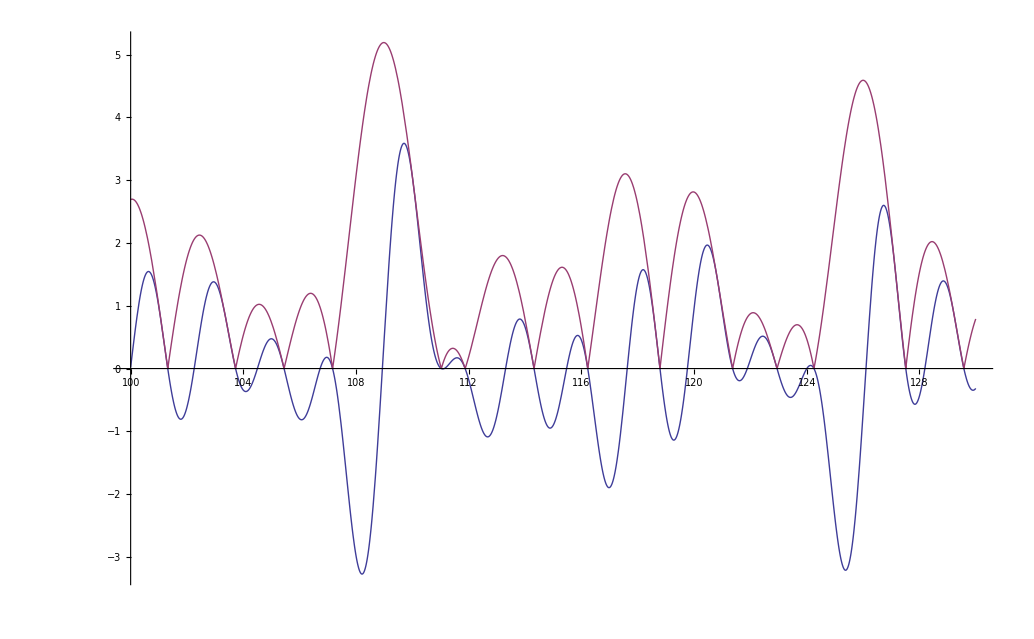

```mathematica
Plot[{ba2[t],Abs[Zeta[1/2+t I]]},{t,100,130}]
```

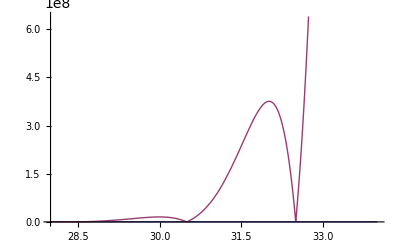

```mathematica
Plot[{0,Abs[ba[I t]]},{t,28,34}]
```

```mathematica
baa[s_]:=(Zeta[1/4-s I]+Zeta[1/4+s I])/2
ba2a[s_]:=(Zeta[1/4-s I]-Zeta[1/4+s I])/(2 I)
```

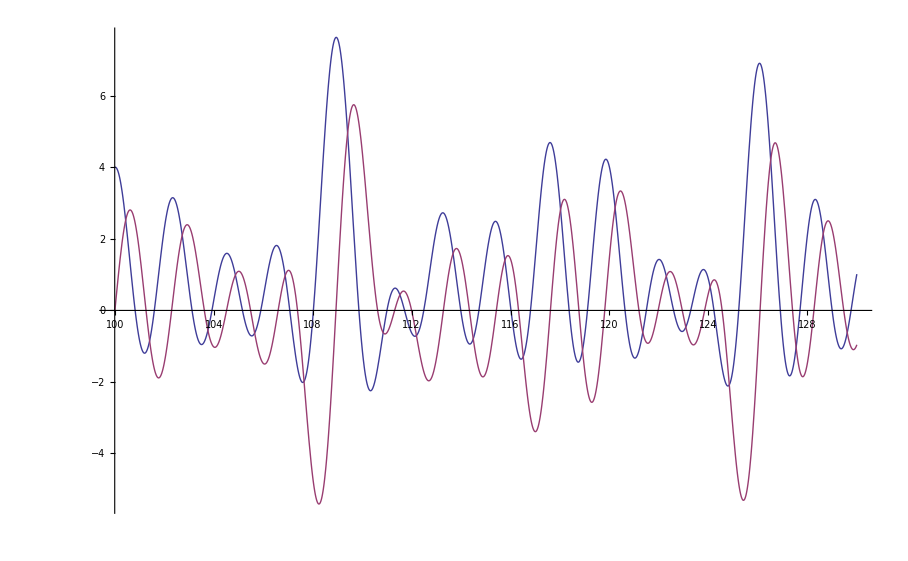

```mathematica
Plot[{baa[t], ba2a[t]},{t,100,130}]
```

```mathematica
pa[t_]:=Cos[t]-2(Cos[t]+2 z Sin[t])/(1+4 z^2)
pa2[t_]:=(Cos[t](1+4 z^2)-2Cos[t]-4 z Sin[t])/(1+4 z^2)
pa3[t_]:=((4 z^2-1)Cos[t]-4 z Sin[t])/(1+4 z^2)
```

```mathematica
pa3[ArcTan[(4z^2-1)/(4z)]]
```

0

```mathematica
FullSimplify[pa3[ArcTan[z-1/(4 z)]]]
```

```mathematica
FullSimplify[Cos[t]-Integrate[Cos[z Log[x]+t]/x^(1/2),{x,0,1}]/.t->ArcTan[z-1/(4z)]]
```

0

```mathematica
$MaxPrecision=1000
$MaxExtraPrecision = 1000
```

1000

1000

```mathematica
bo4[k_]:=D[Zeta[1/2-s]-1+1/(1/2+ s),{s,k}]/.s->0
Table[N[bo4[k],200],{k,0,50}]//TableForm
```

-0.46035450880958681288949915251529801246722933101258149054288608782553052947450062527641937546335681951449637467986952958389234371035889426181923283975376292518263335864916412789122939415410119791731045
-0.077353860790848272528468553285400486269676028493494790431701514745279196849661715119349476895854308596196562011323500315667814398126292033511336744681229969970722917152073207370656202595252565439321651
-0.008357013928661422691306505944962785185593619636354535309295753667809246014498013380680627635638855484923187498947301420447148755692505598154318349064500626738089044617581517255932969840306197174770139
0.0033092453190700973897672206954593025140188465557280542999080656709194418763160340655693246238811201010800734166682492186482620677336540340875288492803670793746998013941211644999014527805344956368126681
0.0026802795525701857266953788154355727038910178233510258092092238126200182968564551670857384812458705254894931579054267598221233836028267815954386483342327614443923260414722143919055275822393438708939266
0.00060066206666342563365592409801332863415701793005835291161639522087328085461588030919781770763062085474116600017281612764421679326672305308008969078400692678969997560470984047942558983714047671913554291
-0.00054653745894605796371590397434310302936451120184607156305932136678520671376740323612466813319776484253771161793971849105935540627892941285604097424170142192763197976675726859820461632471087538321468916
-0.00070262660664312438388776803254796515986970775849368416362295081309268884470888829544209764813657572274525552301465283834158128182044385979527186495290376343311798969178676970330075590211953856074919802
-0.00033760184080139824361245572627885213326427576617218627293585948653543778079390752084921722220006010274489879812085956185250404904946039497724096456601444282210632135882075506434059133440363959134536199
0.00010539708153449920136429387481484248467690018135246829077504332830432207035156482328062437113902882598039790304058662233730288885053793653554423986145743665069077280288859544306467382472972868890047867
0.0003601390899557234666574632429509364198356904045857207127575376278890990304425424774392400518958605234811267431576545559517102998981500449523829391781131682445107270639845630345598209952553418653212941
0.00034524028748512509901258475796457009057546571949600843229663412894338866701363934384492255366157397068075329420331091104830727244190478093003356612749612733873260011131576275032015239100695129150057425
0.00012097854967658662849904339600957356452057428865042743565962960009423137656617313226401324149784311641515048386818796712879048399121645312441700229654990941101237842477322085177493580561249070084066009
-0.0001715022384579342620004372189620023784027599337154510434807156319753494278584858138501394865320296707851819086379772201882077091092017437096871947400446415622565294682007773927520690977944381203494206
-0.00037441645033315363868016512726256049769316590771818858384775626916696563901010178713221314931093194972845685650564667215925126099954240603117910132360813022036931199798174601501819323345114876827332142
-0.00037219473259713347441624506465760010476722037338090921847005516256932300518561156177422577226735610932410478401718225478429456161071861220196608337695700739998336610531119836834081519090684404941990538
-0.00013641771595529886024319815395364046572058622140195446983799505013288820571389713459012414300627447359180738439170811344880196602159426828290522428523858356567030871675224957701072583323656454117458474
0.00025272878787139626047383609789374705748244609077643528714323763876893713172414216823975844909374003704539931494385044697430405931099356884145404080881685340746098096946574769693694671857968192238994003
0.0006178694482317428630268476140376145885653390808009661315458694985397215155145130311530916530326555490117891341603453858073353012125936482835547009228765546443512347992302512296408060167974786289746991
0.00073487354235035253333422746277112302564470742015264876281285550947212516811771344373685112372176717605705062192096816063451429960743128707409221896431019800140415352863190176878599579964576454418271812
0.00042055033706637091770480853262386310331865472475587388780628591601920288451774726472684370981888791779186545717935190383560330058264570997924764706570676494213531567362832235645945601497814194096902983
-0.00035749251603790556030060108732177695106744141540865083662820465139392090563882291009241978973044262302959868141571957763869011473579885311626078567189865473528379839161437431333286664360455320852331437
-0.0013817651439583762427183825979879015165710485286693983013366048810212892018650040171534146508719117982149883366984072348134454749612625472200544651352008225836866958860379580765574350624857853666604784
-0.0021479701657922538833656519139258557242857991466360553926554471193648035824083341669083003618679347140762663045997245169477605816779194254201304746725763116239592193598948612656164229766678155230408484
-0.0019526026495297186381017395263358072065768721199041879364741579538446237897523838794994557971546318000887706247804154585949223411830139860843278094968473041260429912061711400536424795307298544001067892
-0.00015821116109625156270229683833126343527414808094434395702301315510540992040632090282690350805417703428958458744804807853487642062292679585416010562600707017180268903333393822106592548815197744443325961
0.0033559717605729747375920658327359362892435877952396296828537515181698145210604986592490378657566158556371300736635099731705340383766476476277692259053959178177278465535295689691097196707026929154191379
0.0076460652241607695969546725424174962041995340373947183733607982437328612755989550093881973223022151658014066755107156319118436680581954242221395291834790508668989034689588066603748243275337748427855893
0.010294016867855823652059068273600128892787684504454161551715933811880196508887508657199681298460576981324593164762071427831326369257674771003942543370871249355974506047859326687877525551080185243437107
0.0075442718830473493362481397972324495502393194525857816647734606277817260734323278915341827613358111358235315581994463605961153929524411266298560982251626674285931887818915368899631141788204626524997921
-0.0044880892003650225626600633653814855719249450140091997222658732240170100033235107938071138157227003461028283238729864116310663677110203157987589589599536707626672522704675760493168367448887961922073827
-0.027097017565142774686081677008815792592782618964161024249137453900579797333466889078181636427780723092084795432224953708709985039494578263559341678805112822052977322385276520810729317432271282262738665
-0.054812048369935778008901938415227465381805172614872413769549039598944612867539353218555539027433949555505711014268384803609105167291941578492335035120899766559724503887623889365020536514016129765125822
-0.070968882582817233880190220998766795431291905597935461241837722855877420895964676270174411931493547666347185405399095276493698408638480760686740911083358824993427471173305430756880742645236856352469454
-0.046079999674452814208082518903089470469622340819192261352585895250823541690971744512306694111890562328699279094589439247424652593049494684222356790743259735560766695081463416462527090621024300339653182
0.055701341895899117631086068367793816131129711802604493364150218223437963162360605511263259902073258968442728809728989411145856161154371326843373163377244177028629042339201240808864421599882091938989261
0.25529999405621157188712999668057640775464692228976798261438721212936295379769230039505082988323945760102752242752355471146724605812228355141252227100226516582027587959832594180495647342608314581271932
0.51774311072975240243173854316440661441300233431422655900982708982227249285570106954155569512196977187210766147989991069659969239892561340520023061411508474345106701183558758000014489059198799530852821
0.69561746057856236860976305055472340240164942580366201270886211446592269312013710177432019572684255966018998366958162730949806924519587661612429349952287978586366784922505646900178456746654512337300747
0.48168197275081710751296248395060760188157470541279019411468644383207748912362023124757261331918101221390171236022667385531319166217748871668379382140454763016675331639003231216700909443929375211460017
-0.57043835044566352933268031081463343941491262907440102872476485444220130363195693435440096908381062595263061804237574740862631837189492022350958480853786055775603813717839559755277186217063171824195685
-2.8574684984589422554223748369669820943382738468426345075974224474899054927194087308800837413620497838191305660197167796940177363719981211684798407554616964974608437507045289043546288910919029345539007
-6.2475346872444251702286355217979400128379859444662717148420021857169723028716646055958508488824093168561657759490226943376272180833718328978673093856247190678268358869677474361021001221474324933768565
-9.2435814389338120326376022425106630202212372945112646736862296381104907677308597807809226059438605878895618784245256660871603513314178630184176135143114091554107664932718740596990254533999729117205599
-7.9491728219419568744510685778741975539502565241404943243042173512957323981965304126313035347399660758989608781371492029838887985253875637252456009702822307233195912391086635524887286813923485377330356
4.4862708840682596039729888167566430957732624814069182958788014189985776123437802269842820628455033265471366728385886170874879907197658928201745290968962407835477907723116682249962573488589935966821293
36.399743447610999558115408376567828941943187736496809633136880525377578223407244600603877357945825653968731722660221946609618878776149947028161930818937371331658927810507594913091309335042753884308591
91.549681684236337202933124916326309148202121933557996211218552531785765478946937213561385121352482409966285502500840720219544735196300784407709673345099858947676061874031560509104606115885053475409858
155.44098937123301279915307587390365393756318298231604170399212448973937706381552961264483284552283941766159418628329623361630727840301143325082973318203881959571388719053599684170377961098976501849736
172.96805162106867018827579898012881961089139572483711982925451453982806733186622029710570385171925496683121869377415743631356082706986682942605078261566574994099308254263839754842788405883929982509423
23.763123630745759320145161145671042869236489469707080668105373255906904887752752269090205037330808068192307611670802440247585866342605623369831285344902471669433193907859659475857855674653377579317658

```mathematica
bo4[50]
```

68486449405023952496492865790416371950237350107438397655831308926976000000000000+Zeta^(50)[1/2]

```mathematica
Table[N[bo4[k],200],{k,51,100}]//TableForm
```

-481.34483146213122263116623921440336677061098869731678153349124045075063094618435334397847810954013003189168517900300370219370669731357458824691599351871779375919490251302540107524144829088583770173018
-1530.4319504256952044292071531914952587122818123023704936476080216630533901300816513445883762442664870036789416042807771722705936680030930897740414023169493879138826834825002602734843519058212530331763
-3080.1923801209851444529971314111586571731201325813775171150776726141339967915331332737749407848433513561595928095675723607770158065491321636961949409970453053170567130718756067939951408959860223548914
-4366.1978816064606604656383399558185191426623405162026703146125832198451653986118379098121845948421750912611246798352978931046975833830223110496266676828071791991954387124938603814880026606844798939545
-3135.2491234263486698402305882236473402497753283888649545591231252516969506213199235495965248925160885428213720879768882745278962524272821864695570610497904121895408526912717377426465300359029529147771
5114.6998471161440213565495663694055987155598627101624089604980075237340427709769120571943505422443127096635983741819906310639085722026680527023948958329559595126665433938000511910077375767558970453606
26894.394145363252078094837820347422413965763928594057634138632931529946190672553238266644166739802136566383000444704314529804045981529690981405857782415820580258785653169912833439677934122897135083866
67254.854985530303633065451495785421752638341862525661849155349146243715768607195890850243781178601189777114697246453133444274380641194907767482455752531026262648629416133464071857891936921248561265991
119339.22897418822225009506249186835836445137735632735503082777808299996592655743517659038046742803667181984385666999167563522673831249030685125900672000401695351991147952931403929054898800613925737514
142660.7509979533692942208734340245359736566203165759429382330189816586861570323108207916264612468869898598350270041611738992448281376704088514038004197797668096290430108811216945087761242900640976345
29638.402243605631792944951561123653390007783822229709704355298391589934500909508721128636899652926567411291952646332857806084567553180068718916433860369554086520236172792507923619604754772232972563488
-425165.48049444683427536748242775487152490204262551256750387178036055705505481430781466986993387897483369521349171960483554267310774356240260415799416617276950995585827507618010796008718654044220754621
-1.502633308942747166474677196069032273422201215400592381637700695460375939305447812023403457670686297426085080549267053664350015365199611327755144840718636919624458503622989890223087148489449099906415×10^6
-3.3673299741915907089768621233848947660492359378634560601094356871462562163527993605647161306341000567842957272365435906517022728606614342569020242717394744998596708879180336840497365789181077679514518×10^6
-5.5042923731961871929949976306899108331068570252439953957107905168211555953047859587281009906789174312752158568877797491953429877226380252043410818326734737828502591535396749596568221714387775052309919×10^6
-5.5425864534767173497879551580227247596307662618836132234434314544420120850113443390753816741430506984634234894116223591915443440298675941067958569330941131523990125099510892130723610839932486185321541×10^6
2.5752574667168137115151650173417568820601475107746171699845589752181436814027681045227032803967175134292009344148401664614577249827390057832293991341402395116539228167065295168393343704006393353047152×10^6
3.0261824980318538058842965696617853760723507329801122735803866626136840368162712246822516235731357396267338242678666298989762265465808939228082509390776273594663100284647099288896822484039711693200004×10^7
9.2782895829996800889663675168100068687581998987791023610718649586185931447298801639372613371279421996812626115358949132144706562079632311514304302278384074339154672011271408743456466405802749375353877×10^7
1.973365426707593583102913021732912815648120820034404203073423404106836483719489566661718416972790630352056702734079919551005923823627618780260898391390830860465614694345701839755407658290089433830412×10^8
3.0743677723469473231093439349774486545755732532552199608381531329945050395991645627622861578989063610941210941632341156856187454330318235572069339386349480126071975483245998656642371796265289755316769×10^8
2.6639235315151484418870999552645934973292363672819650045995626105218883747189329380597740444623587042872914694206046061173057353764392262766717546091945742808005754184251592932565766562851665133891667×10^8
-3.2629872603627113852026895338268232650126646428871892858246918947020727906343754244613659816459608101084750328987598504268149216038169336318494640936548185262771331477957237379515097637422855054038346×10^8
-2.2357593483716710879088026625471894256246423308844418604574434892982377948551099568100841502091971905556370172699919444059407855127712856417391636043541793160926670570207358721927599955693009230925174×10^9
-6.5044991463185277317856047895650422813145750227978101579622351048845988697266513860929758349455380273550825233140964632921354266556978384089289393261364037366772623455299774817414677213622000583425911×10^9
-1.3628459392044579912557477999303375926450733467295507147449019888764972797714448084156689331449021376970651424437662202060765009093103862001237260973572080583193738582320721733011568035819238125097952×10^10
-2.0959388649231951909156618213916397511850430772775011106321234545573462466012000483679576135299298080511614884099660060950681013111653212070402987781936000648169364689541954560561169405485712540935714×10^10
-1.6841545406721941214827318034364434388526403283504044101196431460162906915574027179733980285012141429014023492524745977706702202545531903938168698354573754831593946329929915531704426776008355071096559×10^10
2.9458496102569667990277939200645831811102772514063538351510097047760930663128054809281363033329642134938803019171292574325409636198932419097312866008159065285640081998641210922926131223071248972778263×10^10
1.7893587453586343717133973759963508227205099751783580820169706538354853739039336877515237196213084945798191169749978607672479515418145184666864796470591421802542790704395893869379817132162819714741951×10^11
5.1956019399215179126506372932471554707705818640903021731567914248630281382399119388255805277764186536161705096115471629052405286438415450410433627180587913396964763287506495743497419319926740644247022×10^11
1.1045230841638481085079663854744864832730756078789813393966510431142361610688944474886822460803062940599697604166008283982772813709052694568653507968299503203993772210357759551827912222551634151262531×10^12
1.7382263185874967254684050328959807682507342502736789393887079649252115118642828165176227799083379297546504832023414616109487846693994115956517384869181877063941678463164490159731330872009201835917051×10^12
1.4584138527466529654802546982629143525805437456357819110610761098537048488314371278207976537138804385423961682503630119245318540391761656031726419104168679188820290668041298874657701301910558920043673×10^12
-2.427128850842059709999225330321095071585361232038855373329093791205844488919253379820350095825780245760101218803809483570371622641126867068861403876355153720599566773595248291962638334127429649454293×10^12
-1.5586912194122948554508580355136448105841587473150566644245853287673857487344465325555898638116568113156370709509547714123041556055872070280177331021972306156072496824046969179374317860372661078664867×10^13
-4.6925585698917843347405869797938051296851616166811224566820127868795815117091717452950021324738619221256782814548538167609019872761714834946879381139942960415120268017954167063369640038169691144054564×10^13
-1.0378863390141401043891016684454217233802388892690808219979493656270837348607002821638072319122958026499963774873549443081798988634684234477854525615445824971088049776724440557041453039481285758633608×10^14
-1.7254115535018195842752373780598031955631193105808584637492285442912144406061657280147663495598006192737842722522916161351372814048521432652648032605024623636521813517796676055044745903998062343218587×10^14
-1.6707076622360929961418805382544151499389933820038471721638057119919027389677560903285259376861099133782160005511861000594803095195434945689577267579078539943190291926581068256144519619228819607288632×10^14
1.7639081636359173996045090311810343115769004588602203563723253848632493143253435685414104211673997679683909597880667415826591173994583479604356353696442444187147672643049792394307296363160304619323644×10^14
1.4580262504763677394426598094934514869285963472716391402511974064947169767088802139464275651197707727126670547002994495445110857972273526728030097211232653254836525469014998577674560070741748101186119×10^15
4.722335445246532595045400426073963986888080881409469633240851939012812817010675435106149574581600270414011169701743035828508519305178623646196108081559534977880234387823699257081822393885012419571496×10^15
1.1109616852612694973137238961761045954970115949899386795287330497290549120688928522072038879955585883985175834893127719591422843982841108243648803751228330383097784029295799050903446592497785288773538×10^16
1.9977800956888390819636472559792106556889583478021341177383114471541544042770088011892331563116698340310160322321840875591723483064773752292447758296066923663075841187713167068551154760965705677319095×10^16
2.3282214872215239296803430113044957928141845657425471666536849741815254583533065674322445525094163713666653131094594578691520911204713799175588292203278729163823609053900407842594422206287823844044431×10^16
-7.1815368745828143536756930548705140020028607218270362772152085011352102114200080429954695197108947793759874440589818625391637568969401784811206309442316342252110310352410714047085341023704519294073044×10^15
-1.4206706362205882131680257691357285930478359589255043233317856675113699049464950929390868797670297985562993374181255329322795064921962399297845196836082221794399196230887888937687389663912370640965009×10^17
-5.1880884651082806308991300970620575646285930179883155122909778663334187556389219602534259121070211054144384453484319552704707260511582305879089057269221707653756596306503125345713497320484534084523678×10^17
-1.3262062044847121210631789212518920026990260332320749775063493274594465346573658082091058939757855934937528067222221729460128223249643041042420729023235864616677745334249967389033905605819521588576131×10^18

```mathematica
-1326206204484712121.0631789212518920026990260332320749775063493274594465346573658082091058939757855934937528067222221729460128223249643041042420729023235864616677745334249967389033905605819521588576131
```

```mathematica
Table[N[bo4[k],30],{k,0,10}]//TableForm
```

-0.460354508809586812889499152515
-0.0773538607908482725284685532854
-0.00835701392866142269130650594496
0.00330924531907009738976722069546
0.00268027955257018572669537881544
0.000600662066663425633655924098013
-0.000546537458946057963715903974343
-0.000702626606643124383887768032548
-0.000337601840801398243612455726279
0.000105397081534499201364293874815
0.000360139089955723466657463242951

```mathematica
TrigToExp@Cos[Log[x]+t]
```

1/2 ⅇ^(-ⅈ t) x^-ⅈ+1/2 ⅇ^(ⅈ t) x^ⅈ

```mathematica
1/2 ⅇ^(-ⅈ t-ⅈ x)+1/2 ⅇ^(ⅈ t+ⅈ x)/.t->-Pi/2
```

1/2 ⅇ^((ⅈ π)/2-ⅈ x)+1/2 ⅇ^(-(ⅈ π)/2+ⅈ x)

```mathematica
FullSimplify[E^(-I t)]
```

ⅇ^(-ⅈ t)

```mathematica
pr[s_,t_]:=(1/2)( E^(t I )Zeta[1/2-s I]+E^(-t I)Zeta[1/2+s I])
```

```mathematica
N@pr[10,4+2I]
```

-3.47072+4.51388 ⅈ

```mathematica
(* ArcTan[n-1/(4 n)] *)
```

```mathematica
Animate[Plot[{Re@pr[n,-t]},{n,0,80},PlotRange->{{0,80},{-4,4}}],{t,0,6.28}]
```

```mathematica
Graphics[{Pink,Disk[]},PlotRange->{{-.5,.5},{0,1.5}},PlotRangeClipping->True,Frame->True]
```

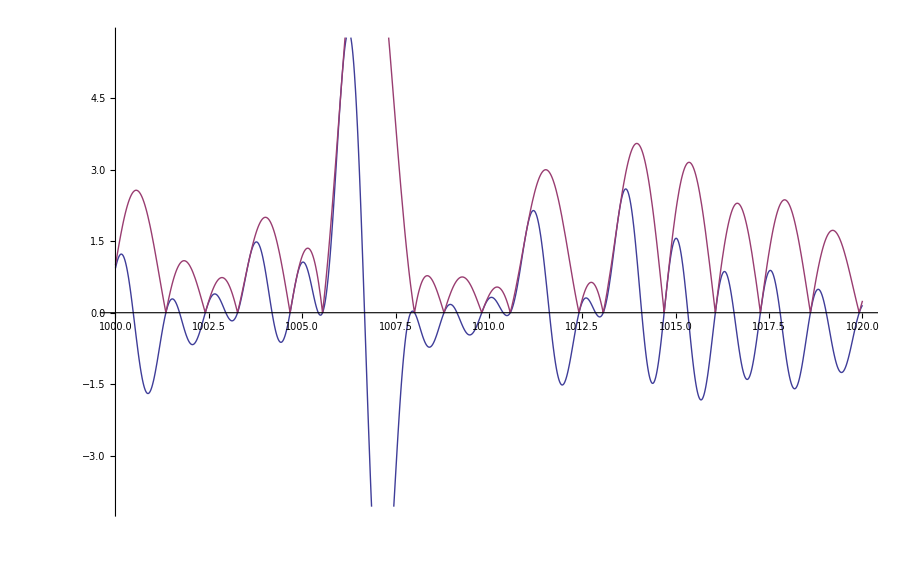

```mathematica
Plot[{pr[z,ArcTan[z-1/(4 z)]],Abs[Zeta[1/2-z I]]},{z,1000,1020}]
```

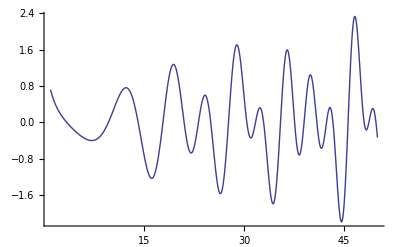

```mathematica
Plot[pr[z,-Pi/2],{z,1,50}]
```

```mathematica
Table[Im[Zeta[1/2-z I]],{z,0,1000,.1}]
```

```mathematica
Table[N[Im@ZetaZero@k],{k,1,300}]
```

$Aborted

```mathematica
Animate[Plot[Cos[n-t],{n,0,50},PlotRange->{{0,50},{-5,5}}],{t,0,6.28}]
```

```mathematica
pr[z,ArcTan[z-1/(4 z)]]
```

1/2 (ⅇ^(-ⅈ ArcTan[1/(4 z)-z]) Zeta[1/2-ⅈ z]+ⅇ^(ⅈ ArcTan[1/(4 z)-z]) Zeta[1/2+ⅈ z])

```mathematica
pr[s_,t_]:=(1/2)( E^(t I )Zeta[1/2-s I]+E^(-t I)Zeta[1/2+s I])
pra[s_,t_]:=Cos[t]Re[Zeta[1/2-s I]]-Sin[t]Im[Zeta[1/2-s I]]
```

```mathematica
pr[7,.3]
```

1.0929+0. ⅈ

```mathematica
pra[7,.3]
```

1.0929

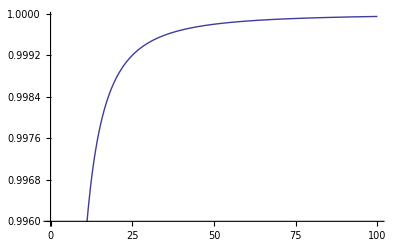

```mathematica
Plot[{1-2/(1+4 z^2)},{z,0,100}]
```

```mathematica
D[Sin[z Log[t]],{z,1}]/.z->0
```

Log[t]

```mathematica
Integrate[ Log[x]/x^(1/2),{x,0,1}]
```

-4

```mathematica
Integrate[ Log[x]^3/x^(1/2),{x,0,1}]
```

-96

```mathematica
Sum[(-1)^k z^(2k+1)/((2k+1)!),{k,0,Infinity}]
```

Sin[z]

```mathematica
sl[z2_]:=Limit[Zeta[1/2-z]-1+1/(1/2+z),z->z2]
```

```mathematica
sl[-1/2]
```

-1+EulerGamma

```mathematica
Zeta[1/2-z]-1+1/(1/2+z)/.z->-s+1/2
```

-1+1/(1-s)+Zeta[s]

```mathematica
1000./ Pi
```

318.31